```mathematica
bisection[f_,a_,b_,eps_]:=(
l=a;r=b;n=0;
While[Abs[r-l]>eps,
If[f[l]*f[(l+r)/2]<0,r=(l+r)/2,l=(l+r)/2];
n++;
];
Print["Bisection Iterations = ",n];
l//N
)
```

```mathematica
newton[f_,a_,b_,eps_]:=(
n=0;
Subscript[x, prev]=a;
Subscript[x, next]=Subscript[x, prev]-(f[Subscript[x, prev]]/(D[f[x],x]/.{x->Subscript[x, prev]}));
While[Abs[Subscript[x, prev]-Subscript[x, next]]>eps,
n++;
Subscript[x, prev]=Subscript[x, next];
Subscript[x, next]=Subscript[x, prev]-(f[Subscript[x, prev]]/(D[f[x],x]/.{x->Subscript[x, prev]}))
];
Print["Newton Iterations = ", n];
Subscript[x, next]//N
)
```

```mathematica
f[x_]=E^x-3
```

-3+ⅇ^x

```mathematica
Log[3]//N
```

1.09861

```mathematica
newton[f,0,10,10^(-4)]
```

Newton Iterations = 5

1.09861

```mathematica
bisection[f,0,10,10^(-4)]
```

Bisection Iterations = 17

1.09856

```mathematica
badF[x_]=x^5+x
```

x+x^5

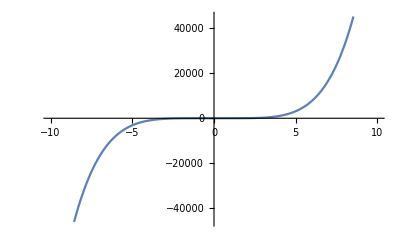

```mathematica
Plot[badF[x],{x,-10,10}]
```

```mathematica
(* newton[badF,-10,10,10^(-3)] *)
```